```mathematica
SetDirectory[NotebookDirectory[]];
dir="/home/drladiges/kumonga/projects/FHDeX/exec/immersedIons/";
(*dir="/home/drladiges/kumongaRoot/scratch/drladiges/results_DISCOS2/WCA_fullwet/";*)
file="potentialDistribution000080000";
raw=Import[dir<>file,"Table"];
binSize = raw[[2,1]]-raw[[1,1]];
```

```mathematica
kb=1.38064852*10^-16;
T=295;

k=50;
vols =Table[ (4/3 π (((2(raw[[ii,1]]+binSize/2))/k)^(3/2)-((2(raw[[ii,1]]-binSize/2))/k)^(3/2))),{ii,1,Length[raw]}];
test=Table[{raw[[ii,1]],raw[[ii,2]] /vols[[ii]]},{ii,1,Length[raw]}];
testNorm=Total[test[[All,2]]];
test2=Table[{test[[ii,1]], test[[ii,2]]/(binSize*testNorm)},{ii,1,Length[test]}];
```

```mathematica
m1=Graphics[{Thick,Red,Circle[{0,0},1]}];
m2=Graphics[{Thick,Blue,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
m3=Graphics[{Thick,Purple,Line[{{-0.5,-0.5},{0.5,0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
m4=Graphics[{Thick,Green,Line[{{0,-0.5},{-0.5,0},{0,0.5},{0.5,0},{0,-0.5}}]}];
```

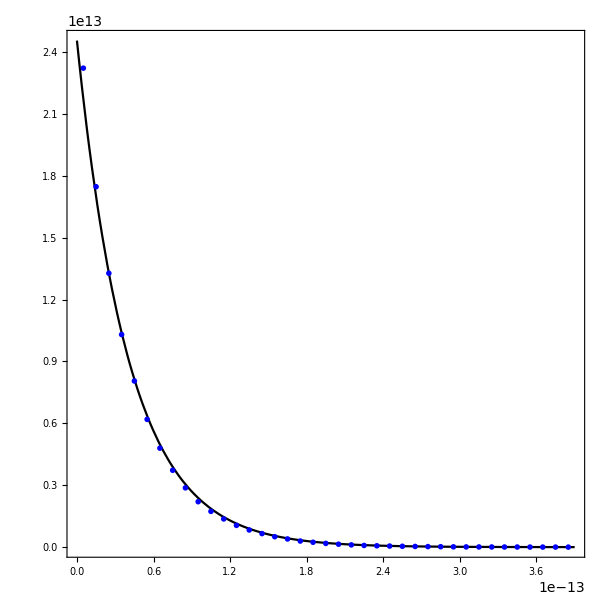

```mathematica
pa=Plot[1/(kb T)Exp[-x/(kb T)],{x,0,3.9*10^-13},PlotRange->All,PlotStyle->Black];
pb=ListPlot[test2,PlotRange->All,PlotStyle->Blue,PlotMarkers->{m2,0.03}];

Show[pa,pb,AspectRatio->1,Frame->True,Axes->False]
```

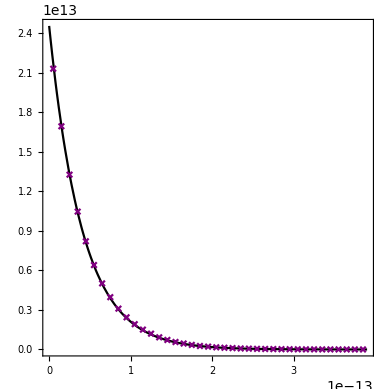
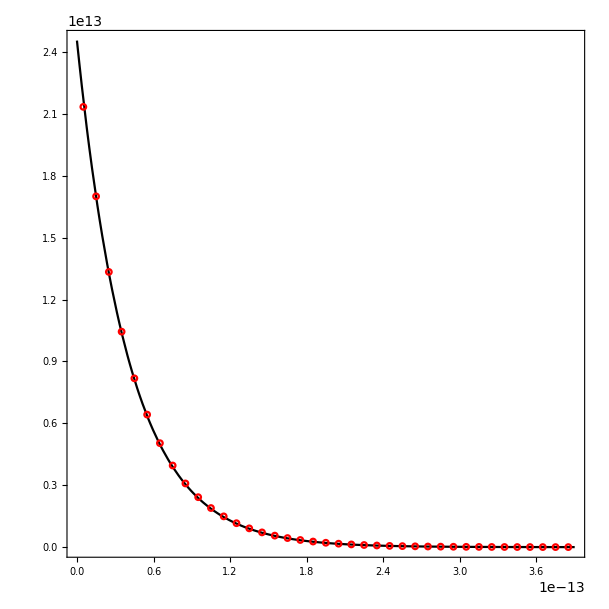
```mathematica
(*wet*)
pa=-Graphics-;
(*damp*)
pb=-Graphics-;
(*dry*)
pc=-Graphics-;
Show[pa,pb,pc]
```